# Building a suite of Learning Analytics Tools for STEM Education

## Aneet Narendranath, PhD, Michigan Technological University Sid Gopujkar (GTA), Michigan Technological University

## #WolframTechConf

## Differing exam performance may be coupled to exam design

```mathematica
SetDirectory[NotebookDirectory[]]
scoreThresh=90; (*Serves as a visualization guide -- guides the eyes*)
data=Import["https://raw.githubusercontent.com/dnaneet/WTC/master/2021/all.csv","CSV"];
data[[1,All]] = Table[data[[All,i]],{i,1,11}];
```

/home/dnaneet/Research_4.0/WTC/2021/actual

### Scores on three Traditional Exams (Spring semester ‘19)

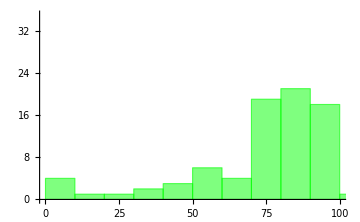
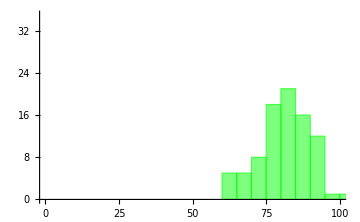
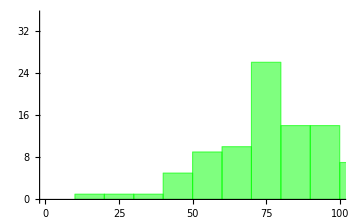

```mathematica
Table[Histogram[data[[All,i]],10,PlotRange->{{0,100},{0,35}},ImageSize->Medium,BaseStyle->{FontSize->20},ChartStyle->Directive[Green]],{i,4,6,1}]
```

### Scores on three Hierarchical Exams (Spring semester ‘21)

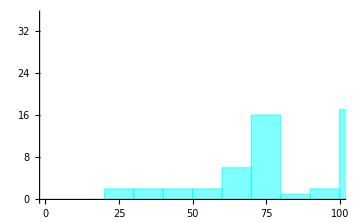
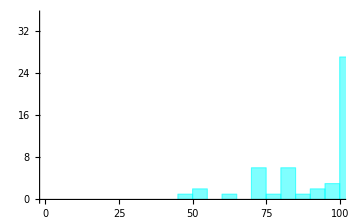
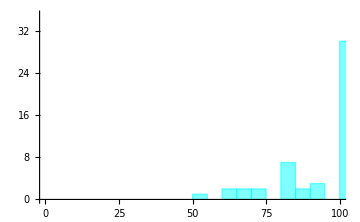

```mathematica
Table[Histogram[data[[All,i]],10,PlotRange->{{0,100},{0,35}},ImageSize->Medium,BaseStyle->{FontSize->20},ChartStyle->Directive[Cyan]],{i,8,10,1}]
```

A greater number of students achieved 100 % on exams that were hierarchical in structure.

## ABSTRACT

I describe part of a learning analytics tool (LAT) that can plug and play into my curriculum.  Using the Wolfram Language, I demonstrate the rationale, creation and operation of a Monte-Carlo sampling type naive, forecast model of student performance on examinations.  Short-term goals for this tool are to use it for systematic design of examinations.  Mid- to long-term goals are to couple it with other tools towards augmenting letter grade assignment process with mastery reports or mastery dashboards.

## Current Story (Pain Point)

Image created with vector graphics from undraw.co

Letter Grades are not representative of mastery, have arbitrary granularity, do not provide adequate feedback to students or adequate actionable intelligence to instructors.   They represent a single, distilled data point with an unstructured support.

## Desired Story (Resolution)

Image created with vector graphics from undraw.co

Student performance on exams results in multi-paradigm data.  It is necessary to “pipeline” all (or as many) different pieces of assessment/performance data generated to create a “more rounded” and “coherent” picture of student/s progress and provide actionable intelligence to an instructor.

## What are the questions I am trying to answer?

## What is the “Value add” to an instructor?

If there is immediate value to an instructor, it is likely that my method would receive less resistance to adoption.

### A-Posteriori Questions with immediate Value

Can an instructor estimate student exam performances with a parametric model thereby creating exams in data driven fashion? This will allow the instructor insight into Critical Incidents during an exam (a) that could map to course content or instruction (b) allow me to provide targeted feedback to individual or groups of students.

What can the instructor do with time on task? This can reveal universally experienced challenges on an exam.

### Future Value add to me as instructor/to my unit

Can systematic construction of exams lead to coherent performance data at a time scale of “weeks”?

Can systematic construction of exams uncover discrete mastery of  concepts levels that can replace arbitrary letter grades?

## Comparison of student performance on traditional vs Hierarchical exam (actual data)

### Scores on three Traditional Exams (Spring semester ‘19)

```mathematica
Table[Histogram[data[[All,i]],10,PlotRange->{{0,100},{0,35}},ImageSize->Medium,BaseStyle->{FontSize->20},ChartStyle->Directive[Green]],{i,4,6,1}]
```

{-Graphics-,-Graphics-,-Graphics-}

### Scores on three Hierarchical Exams (Spring semester ‘21)

```mathematica
Table[Histogram[data[[All,i]],10,PlotRange->{{0,100},{0,35}},ImageSize->Medium,BaseStyle->{FontSize->20},ChartStyle->Directive[Cyan]],{i,8,10,1}]
```

{-Graphics-,-Graphics-,-Graphics-}

A greater number of students achieved 100 % on exams that were hierarchical in structure.

## Replacing Histograms with KDE plots

KDE Plots could present a characteristic curve of student exam performance coupled to assessment structure.

The shape of the KDE plot can be compared across different section of students or semesters that have different n_students.

The shape of the KDE plot is coupled to the underlying exam structure, i.e. “traditional” or “Hierarchical”.

### Traditional exams

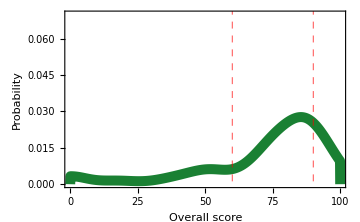
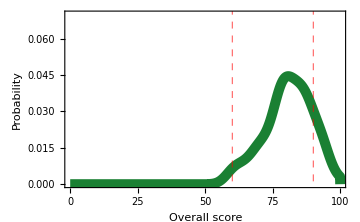
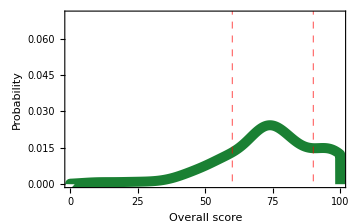

```mathematica
Table[SmoothHistogram[Select[data[[All,i]], NumberQ], PlotRange -> {{0,100}, {0, 0.07}}, PlotStyle -> Directive[{RGBColor[0.1,0.5,0.2],Thickness[0.02]}], 
   GridLines -> {{60, scoreThresh}, None}, GridLinesStyle -> 
    Directive[Red, Dashed], Frame -> True, FrameStyle -> Black, 
   FrameLabel -> {"Overall score", "Probability"},BaseStyle->{FontSize->22},ImageSize->Medium],{i,4,6,1}]
```

### Hierarchical exams

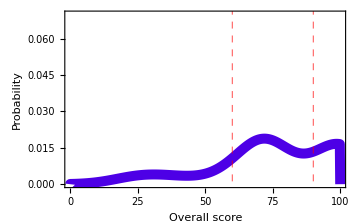
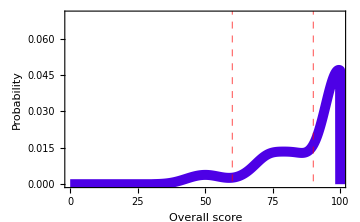
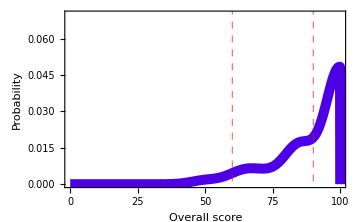

```mathematica
Table[SmoothHistogram[Select[data[[All,i]], NumberQ], PlotRange -> {{0,100}, {0, 0.07}}, PlotStyle -> Directive[{RGBColor[0.3,0.0,0.9],Thickness[0.02]}], 
   GridLines -> {{60, scoreThresh}, None}, GridLinesStyle -> 
    Directive[Red, Dashed], Frame -> True, FrameStyle -> Black, 
   FrameLabel -> {"Overall score", "Probability"},BaseStyle->{FontSize->22},ImageSize->Medium],{i,8,10,1}]
```

## Exam Design Map: Where on this map do exam problems lie?

-Graphics-

## Hierarchical exams (HE) have fewer discrete score levels than traditional exams

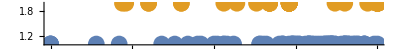
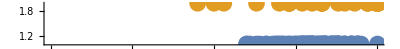
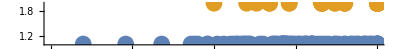

```mathematica
Grid[{{NumberLinePlot[{Select[Round[data[[2;;,4]]],NumberQ],Select[Round[data[[2;;,8]]],NumberQ]},
PlotRange->{{0,100},Automatic},PlotLegends->{"Spring (2019) Exam-1","Spring (2021) Exam-1 (*HE)"},PlotStyle->Directive[PointSize[0.03]]]},

{NumberLinePlot[{Select[Round[data[[2;;,5]]],NumberQ],Select[Round[data[[2;;,9]]],NumberQ]},
PlotRange->{{0,100},Automatic},PlotLegends->{"Spring (2019) Exam-2","Spring (2021) Exam-2 (*HE)"},PlotStyle->Directive[PointSize[0.03]]]},

{NumberLinePlot[{Select[Round[data[[2;;,6]]],NumberQ],Select[Round[data[[2;;,10]]],NumberQ]},
PlotRange->{{0,100},Automatic},PlotLegends->{"Spring (2019) Exam-3","Spring (2021) Exam-3 (*HE)"},PlotStyle->Directive[PointSize[0.03]]]}}]
```

With HEs, each discrete “score” is a signature of mastery of some concept or Bloom’s cognitive level.

## Can we estimate students’ exam performances with a parametric model?

```mathematica
{sp19e1, sp19e2, sp19e3, sp19eF, sp21e1, sp21e2, sp21e3, sp21eF}=Table[PDF[SmoothKernelDistribution[Select[data[[All,i]], NumberQ],"Silverman","Gaussian"], 
    x],{i,4,11}];
```

Since Hierarchical exams are constructed to provide “discrete levels”, it is possible to create a crude yet effective Monte-Carlo sampling function.  This function has a heuristic parameter called “Exam difficulty.”  Driven by this parameter, it can create an ensemble of KDE curves.

#### Forecast KDE curves (Performance Curves) given an exam “difficulty”

```mathematica
pcs = SyntheticPerformanceCurves[0,0,0.6,50,25]; (*pcs: Performance Curves*)
```

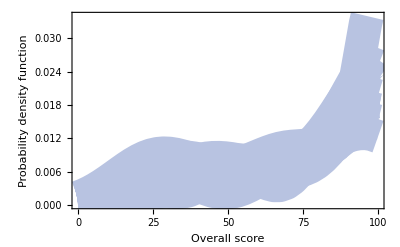

```mathematica
pcsPlot=Plot[pcs,{x,0,100},PlotStyle->Directive[{RGBColor["#B8C3E1"],Thickness[0.06]}],
PlotRange->{{0,100},{0,0.034}},
Frame->True,FrameStyle->Black,MaxRecursion->0,BaseStyle->{FontSize->20}, FrameLabel->{"Overall score","Probability density function"}]
```

## Fitting an ensemble of curves to Exam-1

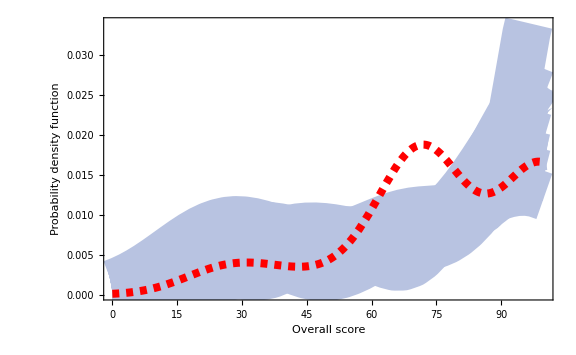

```mathematica
Show[{pcsPlot,Plot[sp21e1,{x,0,100},PlotStyle->{{Red,Dashed,Thickness[0.01]}},GridLines->{{60,scoreThresh},None}, PlotRange->{All,{0,0.07}},PlotLegends->"Expressions",BaseStyle->{FontSize->20}]},ImageSize->Large]
```

## Using the performance curve model to forecast exam-2 and exam-3 performance

I observed that Exam-2 and Exam-3 were of lesser difficulty than exam-1.  They had similar KDE curves.

```mathematica
examDifficultyParameter = 0.3;
pcs = SyntheticPerformanceCurves[0,0,examDifficultyParameter,50,30];
PopupMenu[Dynamic[s],{sp21e1->"Spring 2021 (E1)",sp21e2->"Spring 2021 (E2)",sp21e3->"Spring 2021 (E3)"}]
Manipulate[Show[{PlotSyntheticPerformanceCurve[100,0.07,pcs],
Plot[s,{x,0,100},PlotStyle->{{Red,Dashed,Thickness[0.01]}},GridLines->{{60,scoreThresh},None}, PlotRange->{All,{0,0.07}},PlotLegends->"Expressions",BaseStyle->{FontSize->20}]}],Dynamic[s],ControlType->None]
```

## Story so far ...

The performance curves for exams constructed using a Hierarchical scheme showed a greater number of students with a 100%

A single (heuristic) parameter MC sampling model was created to generate synthetic performance curves.

As students matured into a course (E1 → E2, E3), the exams were “less difficult” as evidenced by actual performance curve compared to the expected performance zone.

## Exam performance in terms of “Time-on-Task”

#### Traditional Exams

“Time-on-task” on exams looks/looked like

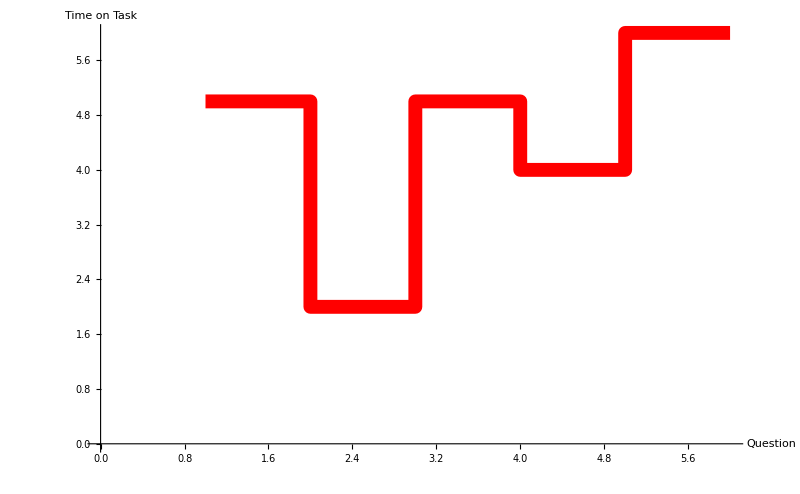

```mathematica
SeedRandom[221];ListStepPlot[RandomInteger[{0,10},5],AxesLabel->{"Question", "Time on Task"},PlotStyle->{Red, Thickness[0.0125]},BaseStyle->{FontSize->26},ImageSize->{800,800}]
```

#### Hierarchical Exams with questions of incremental difficulty

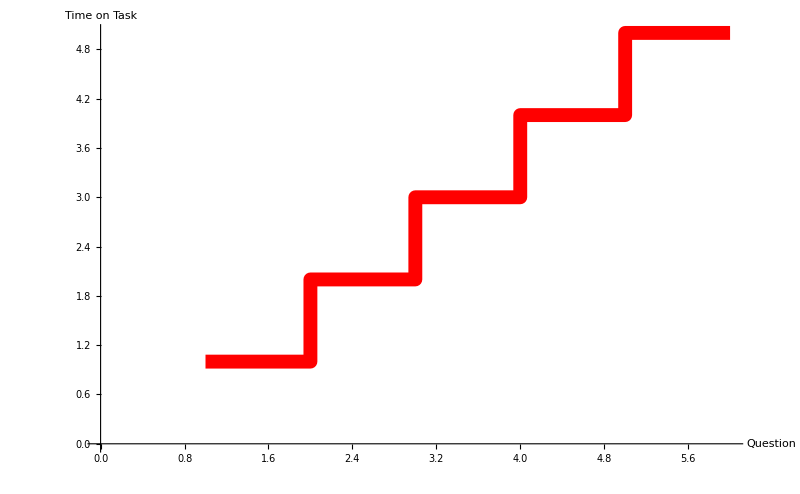

```mathematica
ListStepPlot[Range[5],AxesLabel->{"Question", "Time on Task"},PlotStyle->{Red, Thickness[0.0125]},BaseStyle->{FontSize->26},ImageSize->{800,800}]
```

## The curious case of E1 being more difficult than E2 and E3: Time-on-task metric

```mathematica
E1Time = Import["https://raw.githubusercontent.com/dnaneet/WTC/master/2021/exam_1_time.csv","CSV"];
E2Time = Import["https://raw.githubusercontent.com/dnaneet/WTC/master/2021/exam_2_time.csv","CSV"];
E3Time = Import["https://raw.githubusercontent.com/dnaneet/WTC/master/2021/exam_3_time.csv","CSV"];
```

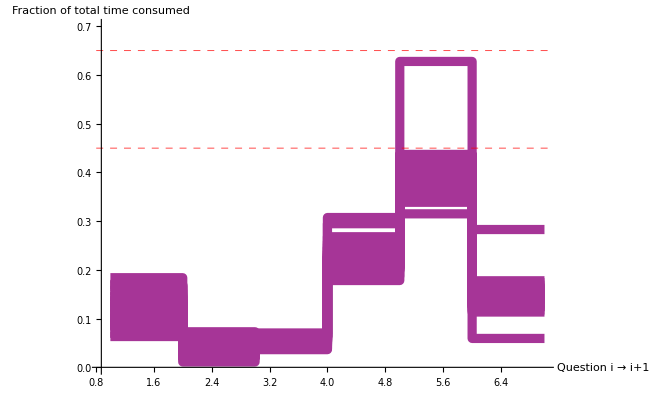

```mathematica
ListStepPlot[TimeOnTask[E3Time],AxesLabel->{"Question i → i+1","Fraction of\ntotal time consumed"},AxesStyle->Black,BaseStyle->{FontSize->16},PlotStyle->Directive[RGBColor["#A63597"],Thickness[0.01]],
GridLines->{None,{.45,.65}},GridLinesStyle->Directive[Red, Dashed],PlotRange->{All,{0,.7}}]
```

What was curious that problem #4 consumed students between 45-70% of the total time they spent on the exam.  Problem #5 (which required greater mastery) consumed less time than problem 4.

## Markov Model for expected "number of attempts" for mastery

This is predicated on that the parametric performance model strongly maps to mastery.

I simulate the performance of a class of 50 students on an exam with difficulty 0.9.  I then replace their discrete scores with mastery levels 1 → 4 (i.e. discrete scores are replaced by cardinal levels 1 -4 via {0→1,50→2, 60→2, 70→3, 80→3, 90→4, 100→4}.

What kind of Markov Model is this?

```mathematica
TransitionMatrix[50,0.3];
MatrixForm@%
```

(0. | 0.08 | 0.14 | 0.78
0. | 0.08 | 0.14 | 0.78
0. | 0. | 0.152174 | 0.847826
0. | 0. | 0. | 1.)

```mathematica
𝒫=DiscreteMarkovProcess[1,pm];
```

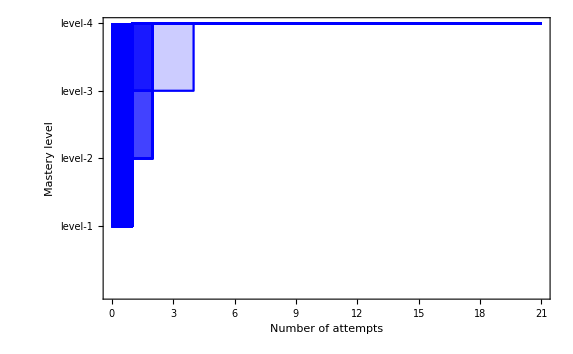

```mathematica
ListStepPlot[Table[RandomFunction[𝒫,{0,20}],50],PlotStyle->Blue,Filling->Top,Frame->True,FrameStyle->Black,
FrameLabel->{"Number of attempts","Mastery level"},
FrameTicks->{{{{1,"level-1"}, {2,"level-2"},{3,"level-3"},{4,"level-4"}},None},{All,None}},BaseStyle->{FontSize->22}]
```

For a given exam difficulty, the ListStepPlot is a signature of how many attempts would the entire class collectively require to attain different mastery levels.

Exams of higher difficulty have larger number of stairs.

## A sneak peak at a performance dashboard

## A sneak peak at KMeans Clustering instead of letter grades

## Summary

## Modules

```mathematica
SyntheticPerformanceCurves0[weight_,hd_, ed_, nStudents_, nCurves_]:=Module[{w=weight,e1 = hd, e2=ed, nstudents=nStudents, ncurves = nCurves},
Table[w Table[If[RandomReal[{0,1}]>e1, 100,RandomInteger[{0,100}]],{i,nstudents}] + (1-w)Table[If[RandomReal[{0,1}]>e2, 100, RandomChoice[{50,60,70,80,90,100}]],nstudents],ncurves]]
```

```mathematica
SyntheticPerformanceCurves[weight_,hd_, ed_, nStudents_, nCurves_]:=Module[{w=weight,e1 = hd, e2=ed, nstudents=nStudents, ncurves = nCurves},
dataTemp=Table[w Table[If[RandomReal[{0,1}]>e1, 100,RandomInteger[{0,100}]],{i,nstudents}] + (1-w)Table[If[RandomReal[{0,1}]>e2, 100, RandomChoice[{20, 30, 40, 50,60,70,80,90,100}]],nstudents],ncurves];
Table[PDF[SmoothKernelDistribution[dataTemp[[i]]],x],{i,1,ncurves,1}]
]

PlotSyntheticPerformanceCurve[xMax_,yMax_,Curve_]:= Module[{xmx=xMax, ymx=yMax, curve=Curve},
Plot[curve,{x,0,xmx},PlotStyle->Directive[{RGBColor["#B8C3E1"],Thickness[0.06]}],
PlotRange->{{0,xmx},{0,ymx}},
Frame->True,FrameStyle->Black,MaxRecursion->0,BaseStyle->{FontSize->20}, FrameLabel->{"Overall score","Probability density function"}]]

TimeOnTask[examTime_]:=Module[{et = examTime},
TimeAccumulate =Accumulate@et[[2;;,2;;]];
Table[N[TimeAccumulate[[i,2;;]]/Total[TimeAccumulate[[i,2;;]]]],{i,1,Length@TimeAccumulate,1}]
]

TransitionMatrix[nStudents_, examDifficulty_]:=Module[{nstudents = nStudents, ed = examDifficulty},
examPerf=Table[If[RandomReal[{0,1}]>ed, 100, RandomChoice[{50,60,70,80,90,100}]],nstudents]/.{0->1,50->2, 60->2, 70->3, 80->3, 90->4, 100->4};
nlevel1 = Count[examPerf,1];
nlevel2 = Count[examPerf,2];
nlevel3 = Count[examPerf,3];
nlevel4= Count[examPerf,4];
pm=N@{{nlevel1/nstudents,nlevel2/nstudents,nlevel3/nstudents,nlevel4/nstudents},
{0,nlevel2/(nlevel2 + nlevel3 + nlevel4),nlevel3/(nlevel2 + nlevel3 + nlevel4),nlevel4/(nlevel2 + nlevel3 + nlevel4)},
{0,0,nlevel3/( nlevel3 + nlevel4),nlevel4/(nlevel3 + nlevel4)},
{0,0,0,nlevel4/nlevel4}
}]
```